# Zestaw 4

## Zadanie 1. Błądzenie przypadkowe w 2D oraz 3D, RandomChoice, Position, oraz inne

Zadanie jest kontynuacją zad. 5 z zestawu nr 3, „Błądzenie przypadkowe w 1D”.
Analogicznie do błądzenia przypadkowego w 1D zdefiniujmy dyskretne błądzenie kulki w dwóch wymiarach.

```mathematica
getSteps[n_]:=RandomChoice[{−1,1}, n];
getWalk[n_]:=Module[
{steps,walk},
steps=getSteps[n];
walk=Accumulate[steps];
walk
]
```

Kulka wykonuje skoki w lewo, w prawo, w dół oraz w górę z takim samym prawdopodobieństwem 0.25.
Przykładowo skok w prawo można przedstawić jako , a skok w górę jako .
Analogicznie do funkcji getSteps[n_] oraz getWalk[n_] dla 1D zdefiniuj funkcje getSteps2D[𝑛𝑛_] oraz getWalk2D[n_] zwracające pozycję kulki po 1, 2, … 𝑛 skokach.

```mathematica
getSteps2D[n_]:=RandomChoice[{{−1,0}, {1,0}, {0,-1}, {0,1}}, n];
getWalk2D[n_]:=Module[
{steps,walk},
steps=getSteps2D[n];
walk=Accumulate[steps];
walk
]
```

```mathematica
getWalk2D[10]
```

{{-1,0},{-2,0},{-2,1},{-2,0},{-2,-1},{-1,-1},{-2,-1},{-3,-1},{-4,-1},{-4,0}}

Sprawdź działanie funkcji getWalk2D przedstawiając jej wynik na wykresie. Użyj w tym celu:

### 1) Funkcji ListLinePlot

Zdefiniuj proporcje wykresu AspectRatio → 1, oraz określ zakres wykresu tak by obejmował kwadratowy obszar ze środkiem w punkcie {0, 0} i by w obszarze tym było widoczne całe błądzenie przypadkowe.
Dla dużego 𝑛 zmniejsz grubość linii korzystając z PlotStyle.

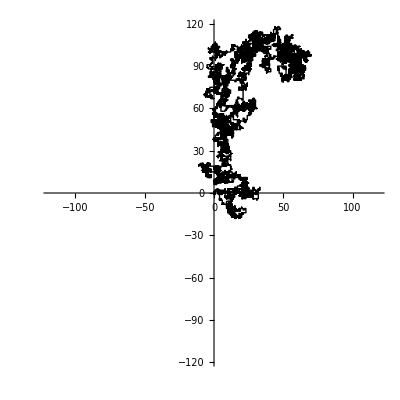

```mathematica
walk = getWalk2D[10 1000];
PlotWalk2D[walk_] := Module[
{maxValue},
maxValue = Max[Abs[walk]];
ListLinePlot[
walk,
AspectRatio -> 1,
PlotStyle-> {Black, Thin},
PlotRange -> {{-maxValue, maxValue}, {-maxValue, maxValue}}
]
];
PlotWalk2D[walk]
```

### 2) Korzystając z opcji Epilog, zaznacz czerwonym punktem pozycję kulki po 𝑛 skokach

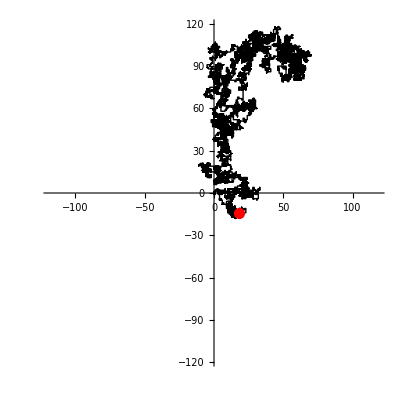

```mathematica
PlotWalk2D[walk_] := Module[
{maxValue},
maxValue = Max[Abs[walk]];
ListLinePlot[
walk,
AspectRatio -> 1,
PlotStyle-> {Black, Thin},
PlotRange -> {{-maxValue, maxValue}, {-maxValue, maxValue}},
Epilog-> {
Red,
PointSize[0.02],
Point[Last[walk]]
}
]
];

PlotWalk2D[walk]
```

### 3) Sprawdź czy dane błądzenie przypadkowe powraca do położenia początkowego

Sprawdź czy dane błądzenie przypadkowe powraca do położenia początkowego, a jeśli tak to po ilu krokach. Wykorzystaj funkcję Position.

```mathematica
?Position
```

```mathematica
Position[walk, {0, 0}]
```

{{2},{4},{6},{8},{10}}

### 4) Stwórz animację błądzenia przypadkowego przy pomocy funkcji Animate

Stwórz animację błądzenia przypadkowego przy pomocy funkcji Animate pokazującą jak przebiega błądzenie przypadkowe w kolejnych skokach od 1 do 𝑛 = 10000.
Wykorzystaj wykres z pkt. 1) dla zwiększającej się liczby pokazanych punktów (skoków). Ta liczba to parametr, który będzie się zmieniał w funkcji Animate.

```mathematica
Animate[
PlotWalk2D[walk[[;;k]]],
{k, 1, Length[walk], 1},
AnimationRunning->False,
DefaultDuration->10,
AnimationRepetitions -> 1
]
```

### 5) Na wykresie w animacji nanieś niebieski punkt w momencie, kiedy błądzenie przypadkowe powróci po raz pierwszy do punktu początkowego

Od tego momentu punkt pozostaje na wykresie. Jeśli błądzenie przypadkowe nie powraca, wtedy punkt się nie pojawia.

```mathematica
PlotAnimationFrame[walk_] := Module[
{maxValue, backAtBegining},
maxValue = Max[Abs[walk]];
backAtBegining = Flatten[Position[walk, {0, 0}]];
ListLinePlot[
walk,
AspectRatio -> 1,
PlotStyle-> {Black, Thin},
PlotRange -> {{-maxValue, maxValue}, {-maxValue, maxValue}},
Epilog-> {
Red,
PointSize[0.02],
Point[Last[walk]],
Blue,
PointSize[Length[backAtBegining] * 0.02],
Point[{0, 0}]
}
]
];
Animate[
PlotAnimationFrame[walk[[;;k]]],
{k, 1, Length[walk], 1},
AnimationRunning->False,
DefaultDuration->10,
AnimationRepetitions -> 1
]
```

### 6) Stwórz analogiczną symulację z dla błądzenia przypadkowego w 3D

```mathematica
movesIn3D = Flatten[Map[
direction |-> {direction, -direction},
{ {1, 0, 0}, {0, 0, 1}, {0, 1, 0} }
], 1]
```

{{1,0,0},{-1,0,0},{0,0,1},{0,0,-1},{0,1,0},{0,-1,0}}

```mathematica
getSteps3D[n_]:=RandomChoice[movesIn3D, n];
getWalk3D[n_]:=Module[
{steps,walk3D},
steps=getSteps3D[n];
walk3D=Accumulate[steps];
walk3D
];
getWalk3D[10]
```

{{0,1,0},{0,1,-1},{0,1,-2},{0,1,-3},{1,1,-3},{1,2,-3},{1,2,-2},{2,2,-2},{2,2,-3},{2,2,-4}}

Użyj ListLinePlot3D. Do naniesienia punktów zamiast Epilog wykorzystaj funkcję Show.

```mathematica
n=2000;
walk3D = getWalk3D[n];
maxValue = Max[Abs[walk3D]];
backAtBegining = Flatten[Position[walk3D, {0, 0, 0}]];

Show[
ListLinePlot3D[
walk3D,
PlotStyle-> {Black, Thin},
AspectRatio->1,
PlotRange -> {{-maxValue, maxValue}, {-maxValue, maxValue}, {-maxValue, maxValue}}
],
Graphics3D[{
Red,
PointSize[0.02],
Point[Last[walk3D]],
Blue,
PointSize[Length[backAtBegining]*0.02],
Point[{0,0,0}]
}]
]
```

-Graphics3D-

## Zadanie 2. Pochodna jako granica, notacja, Limit, D

Pochodną funkcji  w punkcie  nazywamy granicę (o ile istnieje):

Co symbolicznie zapisuje się m.in. jako , , , , .
Jeśli pochodna jest po czasie spotyka się też zapis .

Policz pochodną dla przykładowej funkcji  korzystając z różnych notacji w Mathematica®:

```mathematica
Clear[n];
f[x_] = a x^n
```

a x^n

### 1) skorzystaj z funkcji Limit by zdefiniować funkcję fD[f_, x_] liczącą pochodną 𝑓 z definicji

```mathematica
?Limit
```

```mathematica
fD[f_, x_] := Limit[
(f[x + dx] - f[x]) / dx,
dx -> 0
]
fPrim = fD[f, x]
```

a n x^(-1+n)

### 2) skorzystaj z wbudowanej funkcji D

Zapoznaj się z jej składnią.

```mathematica
?D
```

```mathematica
D[f[x], x]
```

a n x^(-1+n)

### 3) policz pochodną drugiego, trzeciego, k-tego rzędu korzystając z D

```mathematica
D[f[x], {x, 2}]
```

a (-1+n) n x^(-2+n)

```mathematica
D[f[x], {x, 3}]
```

a (-2+n) (-1+n) n x^(-3+n)

```mathematica
D[f[x], {x, k}]
```

a x^(-k+n) FactorialPower[n,k]

### 4) skorzystaj z zapisu f'[x], f''[x], f'''[x]

```mathematica
f'[x]
```

a n x^(-1+n)

```mathematica
f''[x]
```

a (-1+n) n x^(-2+n)

```mathematica
f'''[x]
```

a (-2+n) (-1+n) n x^(-3+n)

### 5) skorzystaj z Derivative[rząd_pochodnej_][funkcja_]

```mathematica
Derivative[2][f]
Derivative[3][f]
Derivative[k][f]
```

a (-1+n) n #1^(-2+n)&

a (-2+n) (-1+n) n #1^(-3+n)&

a FactorialPower[n,k] #1^(-k+n)&

Ciekawostka:
W poleceniu Derivative ujemny rząd pochodnej będzie reprezentował całkę nieoznaczoną odpowiedniego rzędu z zadanej funkcji.

```mathematica
Derivative[-1][f]
```

(a #1^(1+n))/(1+n)&

## Zadanie 3. Pochodna i jej własności, D

Teraz skorzystaj z wbudowanej funkcji D by policzyć następujące pochodne dla funkcji oraz :

### 1) pochodna sumy funkcji

```mathematica
D[fA[x] + fB[x], x]
```

fA'[x]+fB'[x]

### 2) pochodna iloczynu funkcji

```mathematica
D[fA[x] * fB[x], x]
```

fB[x] fA'[x]+fA[x] fB'[x]

### 3) pochodna odwrotności funkcji

```mathematica
D[1 / fA[x], x]
```

-fA'[x]/fA[x]^2

### 4) pochodna ilorazu funkcji

```mathematica
FullSimplify[D[fA[x] / fB[x], x]]
```

(fB[x] fA'[x]-fA[x] fB'[x])/fB[x]^2

### 5) pochodna złożenia funkcji

```mathematica
D[fA[fB[x]], x]
```

fA'[fB[x]] fB'[x]

## Zadanie 4. Pochodne w punkcie, D

Obliczyć pochodne do 6-tego rzędu dla funkcji.
Podać wartość dokładną, a następnie przybliżoną z użyciem N.

### 1) w punkcie

```mathematica
Derivative[6][Function[x, x^x]][1]
```

54

### 2) w punkcie

```mathematica
result = FullSimplify[
Derivative[6][Function[x, Log[x / (x+E)^2] ^ 4]][E]
]
```

(15 (1+Log[4]) (167+Log[4] (223+62 Log[4])))/(2 ⅇ^6)

```mathematica
N[result]
```

26.409

```mathematica
FullSimplify[res]
```

res

## Zadanie 5. Pochodna jako styczna w punkcie, D, Plot

Znaleźć równanie stycznej do wykresu funkcji  w punkcie .

```mathematica
f[x_] = Sin[x];
x0 = 2;
sA = f'[x0];
sB = f[x0] - sA x0;
s[x_] = sA x + sB
```

-2 Cos[2]+x Cos[2]+Sin[2]

Przedstawić na wykresie funkcję , wyznaczoną styczną oraz zaznaczyć punkt styczności. Proszę wykonać wykres w zakresie .

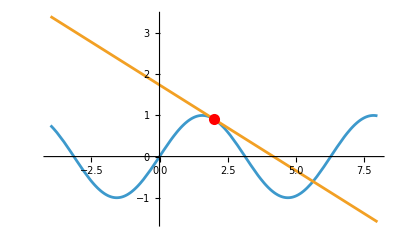

```mathematica
Plot[
{f[x], s[x]},
{x, -4, 8},
Epilog -> {
Red,
PointSize[0.02],
Point[{x0, f[x0]}]
}
]
```